```mathematica
notation = {wAe ->Subscript[w, A,e], wAg -> Subscript[w, A,g], wBe ->Subscript[w, B,e], wBg -> Subscript[w, B,g], wsec -> Subscript[w, sec] , wA->Subscript[w, A], wB->Subscript[w, B], delta->Δ, hb->ℏ, uA->Subscript[u, A], uB -> Subscript[u, B], n->η};
```

```mathematica
H0 =DiagonalMatrix[{wAe+wBe+wsec, wAe+wBe, wAe+wBg+wsec, wAe+wBg, wAg +wBe+wsec, wAg +wBe, wAg +wBg+wsec,wAg + wBg}]; MatrixForm[H0] /. notation
```

(w_sec+w_(A,e)+w_(B,e) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | w_(A,e)+w_(B,e) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | w_sec+w_(A,e)+w_(B,g) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | w_(A,e)+w_(B,g) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | w_sec+w_(A,g)+w_(B,e) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | w_(A,g)+w_(B,e) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | w_sec+w_(A,g)+w_(B,g) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | w_(A,g)+w_(B,g))

```mathematica
H1 = {{0,0,uB E0/2 Exp[-I wB t],0,0,n uA E0/2 Exp[-I wA t],0,0},
{0,0,n uB E0/2 Exp[-I wB t],0,0,uA E0/2 Exp[-I wA t],0,0},
{uB E0/2 Exp[I wB t],n uB E0/2 Exp[I wB t],0,0,0,0,0,n uA E0/2 Exp[-I wA t]},
{0,0,0,0,0,0,0,uA E0/2 Exp[-I wA t]},
{0,0,0,0,0,0,uB E0/2 Exp[-I wB t],0},
{n uA E0/2 Exp[I wA t],uA E0/2 Exp[I wA t],0,0,0,0,n uB E0/2 Exp[-I wB t],0},
{0,0,0,0,uB E0/2 Exp[I wB t],n uB E0/2 Exp[I wB t],0,0},
{0,0,n uA E0/2 Exp[I wA t],n uA E0/2 Exp[I wA t],0,0,0,0} }; MatrixForm[H1] /. notation
```

(0 | 0 | 1/2 ⅇ^(-ⅈ t w_B) E0 u_B | 0 | 0 | 1/2 ⅇ^(-ⅈ t w_A) E0 η u_A | 0 | 0
0 | 0 | 1/2 ⅇ^(-ⅈ t w_B) E0 η u_B | 0 | 0 | 1/2 ⅇ^(-ⅈ t w_A) E0 u_A | 0 | 0
1/2 ⅇ^(ⅈ t w_B) E0 u_B | 1/2 ⅇ^(ⅈ t w_B) E0 η u_B | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t w_A) E0 η u_A
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t w_A) E0 u_A
0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t w_B) E0 u_B | 0
1/2 ⅇ^(ⅈ t w_A) E0 η u_A | 1/2 ⅇ^(ⅈ t w_A) E0 u_A | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t w_B) E0 η u_B | 0
0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t w_B) E0 u_B | 1/2 ⅇ^(ⅈ t w_B) E0 η u_B | 0 | 0
0 | 0 | 1/2 ⅇ^(ⅈ t w_A) E0 η u_A | 1/2 ⅇ^(ⅈ t w_A) E0 η u_A | 0 | 0 | 0 | 0)

```mathematica
U0 = DiagonalMatrix[Exp[-I {wAe+wBe+wsec, wAe+wBe, wAe+wBg+wsec, wAe+wBg, wAg +wBe+wsec, wAg +wBe, wAg +wBg+wsec,wAg + wBg} t]];
MatrixForm[U0] /. notation
```

(ⅇ^(-ⅈ t (w_sec+w_(A,e)+w_(B,e))) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-ⅈ t (w_(A,e)+w_(B,e))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(-ⅈ t (w_sec+w_(A,e)+w_(B,g))) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-ⅈ t (w_(A,e)+w_(B,g))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (w_sec+w_(A,g)+w_(B,e))) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (w_(A,g)+w_(B,e))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (w_sec+w_(A,g)+w_(B,g))) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (w_(A,g)+w_(B,g))))

```mathematica
V = Inverse[U0].H1.U0; V = V/.{wA->wAe - wAg +wsec - delta, wB -> wBe -wBg -wsec - delta} // FullSimplify;MatrixForm[V] /.notation
```

(0 | 0 | 1/2 ⅇ^(ⅈ t (Δ+w_sec)) E0 u_B | 0 | 0 | 1/2 ⅇ^(ⅈ t Δ) E0 η u_A | 0 | 0
0 | 0 | 1/2 ⅇ^(ⅈ t Δ) E0 η u_B | 0 | 0 | 1/2 ⅇ^(ⅈ t (Δ-w_sec)) E0 u_A | 0 | 0
1/2 ⅇ^(-ⅈ t (Δ+w_sec)) E0 u_B | 1/2 ⅇ^(-ⅈ t Δ) E0 η u_B | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t Δ) E0 η u_A
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t (Δ-w_sec)) E0 u_A
0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t (Δ+w_sec)) E0 u_B | 0
1/2 ⅇ^(-ⅈ t Δ) E0 η u_A | 1/2 ⅇ^(-ⅈ t (Δ-w_sec)) E0 u_A | 0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t Δ) E0 η u_B | 0
0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t (Δ+w_sec)) E0 u_B | 1/2 ⅇ^(-ⅈ t Δ) E0 η u_B | 0 | 0
0 | 0 | 1/2 ⅇ^(-ⅈ t Δ) E0 η u_A | 1/2 ⅇ^(-ⅈ t (Δ-w_sec)) E0 η u_A | 0 | 0 | 0 | 0)

```mathematica
densitym= Table[Subscript[p, i,j][t], {i,8}, {j,8}]; MatrixForm[densitym]
```

(p_(1,1)[t] | p_(1,2)[t] | p_(1,3)[t] | p_(1,4)[t] | p_(1,5)[t] | p_(1,6)[t] | p_(1,7)[t] | p_(1,8)[t]
p_(2,1)[t] | p_(2,2)[t] | p_(2,3)[t] | p_(2,4)[t] | p_(2,5)[t] | p_(2,6)[t] | p_(2,7)[t] | p_(2,8)[t]
p_(3,1)[t] | p_(3,2)[t] | p_(3,3)[t] | p_(3,4)[t] | p_(3,5)[t] | p_(3,6)[t] | p_(3,7)[t] | p_(3,8)[t]
p_(4,1)[t] | p_(4,2)[t] | p_(4,3)[t] | p_(4,4)[t] | p_(4,5)[t] | p_(4,6)[t] | p_(4,7)[t] | p_(4,8)[t]
p_(5,1)[t] | p_(5,2)[t] | p_(5,3)[t] | p_(5,4)[t] | p_(5,5)[t] | p_(5,6)[t] | p_(5,7)[t] | p_(5,8)[t]
p_(6,1)[t] | p_(6,2)[t] | p_(6,3)[t] | p_(6,4)[t] | p_(6,5)[t] | p_(6,6)[t] | p_(6,7)[t] | p_(6,8)[t]
p_(7,1)[t] | p_(7,2)[t] | p_(7,3)[t] | p_(7,4)[t] | p_(7,5)[t] | p_(7,6)[t] | p_(7,7)[t] | p_(7,8)[t]
p_(8,1)[t] | p_(8,2)[t] | p_(8,3)[t] | p_(8,4)[t] | p_(8,5)[t] | p_(8,6)[t] | p_(8,7)[t] | p_(8,8)[t])

```mathematica
Relax = DiagonalMatrix[{GA+GB, GA+GB, GA,GA,GB,GB,0,0}];
```

```mathematica
lhs = Flatten[D[densitym,t]];
rhs1 = Flatten[Simplify[-I/hb *(V.densitym-densitym.V)]];
rhs2 = Flatten[-1/2(Relax.densitym + densitym.Relax)];
rhs3 = Flatten[DiagonalMatrix[{0,0,GB Subscript[p, 1,1][t],GB Subscript[p, 2,2][t],GA Subscript[p, 1,1][t],GA Subscript[p, 2,2][t],GA Subscript[p, 3,3][t]+GB Subscript[p, 5,5][t], GA Subscript[p, 4,4][t]+GB Subscript[p, 6,6][t]}]];
eqlist = Thread[lhs == rhs1+rhs2 + rhs3];
```

```mathematica
initial = Thread[Flatten[Table[Subscript[p, i,j][0], {i,8}, {j,8}]] == Flatten[DiagonalMatrix[{0,0,0,0,0,0,0,1}]]];
```

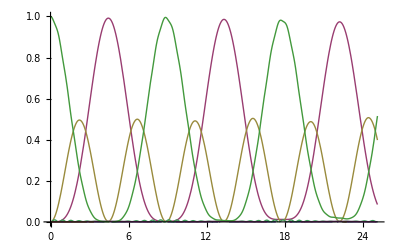

```mathematica
solution = {Subscript[p, 1,1][t], Subscript[p, 2,2][t], Subscript[p, 3,3][t], Subscript[p, 4,4][t],Subscript[p, 5,5][t], Subscript[p, 6,6][t], Subscript[p, 7,7][t], Subscript[p, 8,8][t]} /. NDSolve[ Join[eqlist, initial] /.{E0->1,n->1, uA->1, uB->1, delta->0, hb->1, GA->0, GB->0, wsec->10}, Flatten[densitym], {t,0,8*Pi}];Plot[solution, {t,0,8*Pi}, PlotRange->All]
```

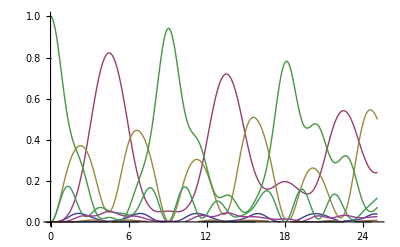

```mathematica
solution = {Subscript[p, 1,1][t], Subscript[p, 2,2][t], Subscript[p, 3,3][t], Subscript[p, 4,4][t],Subscript[p, 5,5][t], Subscript[p, 6,6][t], Subscript[p, 7,7][t], Subscript[p, 8,8][t]} /. NDSolve[ Join[eqlist, initial] /.{E0->1,n->1, uA->1, uB->1, delta->0, hb->1, GA->0, GB->0, wsec->2}, Flatten[densitym], {t,0,8*Pi}];Plot[solution, {t,0,8*Pi}, PlotRange->All]
```

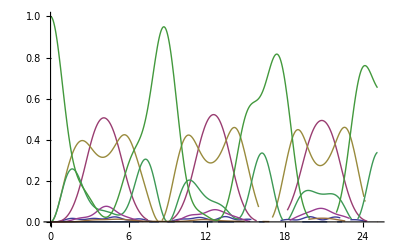

```mathematica
solution = {Subscript[p, 1,1][t], Subscript[p, 2,2][t], Subscript[p, 3,3][t], Subscript[p, 4,4][t],Subscript[p, 5,5][t], Subscript[p, 6,6][t], Subscript[p, 7,7][t], Subscript[p, 8,8][t]} /. NDSolve[ Join[eqlist, initial] /.{E0->1,n->1, uA->1, uB->1, delta->0.5, hb->1, GA->0, GB->0, wsec->2}, Flatten[densitym], {t,0,8*Pi}];Plot[solution, {t,0,8*Pi}, PlotRange->All]
```